```mathematica
reg[[181, 1]]
```

{109119604060725664814308901024268869132,4,1}

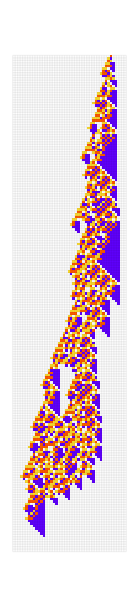
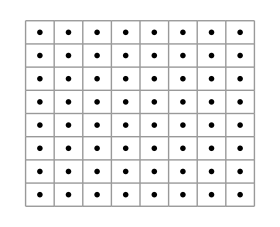

```mathematica
Row[{ArrayPlot[ArrayPad[CellularAutomaton[{109119604060725664814308901024268869132,4,1},{{1},0},200],{{0,0},{3,3}}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"],ImageSize->{Automatic,520},Mesh->All,MeshStyle->Opacity[.05]],RulePlot[CellularAutomaton[{109119604060725664814308901024268869132,4,1}],ColorRules->{{"[◼]", "CustomStyleData"}}["Colors"]][[1,1,All,All,1]]//Flatten//Partition[#,UpTo[8]]&//GraphicsGrid[#,Dividers->Directive[Thin,GrayLevel[.6]],ImageSize->280]&},Spacer[20]]
```

```mathematica
SymIndexMap[k_,r_]:=SymIndexMap[k,r]=With[
{tups=Tuples[Reverse[Range[0,k-1]],2r+1]},
Sort[Catenate[MapIndexed[{Position[tups,#][[1,1]],#2[[1]]}&,
GatherBy[tups,Sort[{#,Reverse[#]}]&],{2}]]]
]
```

```mathematica
SymUp[k_,r_]:=SymUp[k,r
]=SymIndexMap[k,r][[All,2]]
```

```mathematica
SymDown[k_,r_]:=SymDown[k,r
]=Values[KeySort[Map[First,
GroupBy[SymIndexMap[k,r],
Last->First]]]]
```

```mathematica
RandomRuleMutation[{rn_,k_,r_},
many_Integer:1,
OptionsPattern[{"Symmetric"->False}]
]:=Module[
{up,down,cases},
{up,down}=If[
TrueQ[OptionValue["Symmetric"]],
{SymUp[k,r],SymDown[k,r]},
{All,All}
];
cases=IntegerDigits[rn,k,k^(2r+1)][[down]];
{FromDigits[#[[up]],k],k,r}&[
MapAt[Mod[#+RandomInteger[{1,k-1}],k]&,
cases,List/@RandomSample[1;;Length[cases]-1,many]]
] 
]
```

```mathematica
evo = Module[
{deep=2000,cut=200,ru,life,evo,data},
SeedRandom[426778+181];
evo=NestList[CompoundExpression[
ru=RandomRuleMutation[First[#]],
life={{"[◼]", "TestLifetime"}}[ru,cut],
If[life>=Last[#],{ru,life},#]
]&,{{0,4,1},0},deep]
];
```

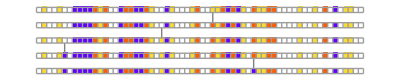
-Graphics-
⋮
-Graphics-
⋮

```mathematica
Column[{{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[evo][[1;;5,1]],"Arrows"->"Line",ImageSize->400],"⋮",{{"[◼]", "RulesMutationPlot"}}[DeleteDuplicates[evo][[100;;104,1]],"Arrows"->"Line",ImageSize->400],"⋮"},Center]
```